# 1-D universal estimator using DNN

## Generating data

Generates synthetic data for DNN :

Arguments:
	n: number of samples drawn for a given θ 
	M: number of different θ generated in the range [min_θ, max_θ]
	S: number of samples per θ (number of calls to yulesimon.rvs with same θ)
	f: the distribution function for generating samples. f(θ, N) returns N observations using parameter θ
	range: range of the dist parameter θ
	bins: number of bins in the histograms generated from samples
Return:
	a table of associations(one row per sample): histogram->θ

```mathematica
GenerateData[M_, n_, S_, f_, range_, bins_:-1]:=
	Module[{params, samples, nbins, MAXBINS, expansion, initparams},
		initparams=Table[RandomReal[{range[[1]],range[[2]]}],{i,1,M}];
		(*generate M different random initparameters in the range [min_θ,max_θ]*)
		expansion[j_]:=Table[initparams[[j]],S]; 
		(*define an expansion function for duplicating the initparameters*)
		params=Flatten[Table[expansion[w],{w,1,M}]];
		(*increase the number of each different parameters to S, now we have M*S params *)
		samples=Table[f[params[[i]],n],{i,1,M*S}];
		(*generate M*S distributions, each distribution has n number/data, now we have M*S*n data*)
		MAXBINS=5000;
		nbins=If[bins>0,bins,Min[MAXBINS, Ceiling[Max[samples]]+1](*Ceiling[Max[samples]]+2] if using zero padding*)];
		h[x_]:=N[Log10[HistogramList[x,{0,nbins,1}][[2]]+1]]; (* using log10(x+1)*)
		Table[h@samples[[i]]->params[[i]], {i,1,M*S}]  
	
	]
```

## Example of generated data

```mathematica
(*f[å_,N_]:=RandomVariate[WaringYuleDistribution[å],N];
Print[GenerateData[5,10,3,f,{2,3}]//TableForm];*)(*without logging the histogram*)
```

{10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}→2.93413
{7,2,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0}→2.93413
{7,2,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0}→2.93413
{7,1,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0}→2.34788
{6,2,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0}→2.34788
{6,1,1,1,0,0,0,1,0,0,0,0,0,0,0,0,0}→2.34788
{8,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0}→2.82276
{8,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}→2.82276
{9,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0}→2.82276
{5,3,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1}→2.10973
{8,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0}→2.10973
{8,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0}→2.10973
{7,2,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0}→2.65129
{6,1,2,1,0,0,0,0,0,0,0,0,0,0,0,0,0}→2.65129
{7,2,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0}→2.65129

## DNN

Generate a DNN for predicting the parameter θ from the distribution histogram
The NN is fully connected, the input size is the number of bins in the input histogram, the output is a scalar predicting the parameter used to generate the input sample.

```mathematica
CreateNet[bins_]:=( 
NetChain[{
LinearLayer[bins],  
BatchNormalizationLayer[],  (*batch normaliztiozion*)
ElementwiseLayer[Ramp], (*Ramp is the relu*)

LinearLayer[bins], 
BatchNormalizationLayer[],
ElementwiseLayer[Ramp], 


LinearLayer[bins], 
BatchNormalizationLayer[],
ElementwiseLayer[Ramp], 


LinearLayer[1]
},
"Input"->bins, 
"Output" -> "Scalar"]
)
```

## 1-D universal estimator using DNN

Given a distribution  dist(x|θ) and the range for the parameter θ,  
UniversalEstimator returns an Estimator function for predicting the parameter θ given an input sample S.

```mathematica
UniversalEstimator[dist_, range_]:=Module[{g, M, n, S, trainSet, bins, valSet ,net, trained, model, h},
(*define a sample generator*)
g[θ_,n_] := RandomVariate[dist[θ],n];

(*train a NN for predicting the parameter θ *)
(*generate learning samples in the the given parameter range*)
M = 100; 
S = 100;  (* M*S is the number of learning samples*)
n = 1024;   (*number of observations in each sample*)
trainSet=GenerateData[M,n,S, g, range];
bins = Length@trainSet[[1]][[1]]; (*use the same number of bins for the validation set*)
valSet=GenerateData[M/2,n, S, g, range, bins];

(*Create and train the NN*)
net = NetInitialize@CreateNet[bins];

trained=NetTrain[
net,
trainSet,
All,
ValidationSet->valSet, 
TrainingStoppingCriterion-><|"Criterion"->"Loss","Patience"->500|>, (*using loss criterion to prevent overfitting*)
Method->"ADAM" ,
BatchSize->1024

];

Print[trained];  (*print the training result*)

model = trained["TrainedNet"];

(*define a function for generating a histogram with nbins from an input sample )*)
h[x_]:=N[Log10[HistogramList[x,{0,bins,1}][[2]]+1]];

(*return an Estimator which is a fucntion map sample to a parameter*)
Function[{sample}, (
(*return a prediction of the parameter θ*)
model[h@sample]
)]
]
```

## Experiment of universal estimator with DNN

n : number of samples drawn for a given θ 
M : number of different θ generated in the range [min_θ, max_θ]
S : number of samples per θ

```mathematica
RunExperiment[dist_, range_]:= Module[{estimator, g, adjuster, params, n, samples, Θ, Θhat, e, TestSet, M, initΘ, expansion,S},
(*generate an Estimator for dist*)
estimator = UniversalEstimator[dist, range];
(*define the size of the test set*)
M = 20;
S = 10；
n = 1024;

initΘ=Table[RandomReal[{range[[1]],range[[2]]}],{i,1,M}];
(*generate M different random initΘ in the range [min_θ,max_θ]*)
expansion[j_]:=Table[initΘ[[j]],S]; 
(*define an expansion function for duplicating the initΘ*)
Θ=Flatten[Table[expansion[w],{w,1,M}]];
(*increase the number of each different parameters to S, now we have M*S Θ *)		
g[θ_,a_] := RandomVariate[dist[θ],a];
(*create M*S test samples*)
samples = Table[g[Θ[[i]], n], {i,1,M*S,1 }];

(*predict the parameter for each sample*)
Θhat = Table[estimator[samples[[i]]], {i,1,M*S,1 }];

(*evaluate prediction errors*)

e = Table[Abs[Θ[[i]] - Θhat[[i]]], {i,1,M*S,1 }];

Print["θ: ",Θ];
Print["θ̂: ",Θhat];
Print["abs(θ-θ̂): ",e];
Print["RMSE:",RootMeanSquare[e]];

(*return true parameters and predicted errors*)
{Θ, e}
]
```

## Run the experiment for the different distributions

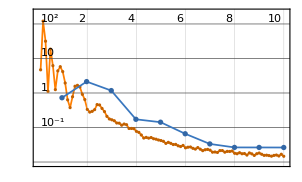
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:100  rounds:10  time:1.4min  examples/s:1183
data | ,,  training examples:10000  validation examples:5000  processed examples:102400  skipped examples:0
method | ,,  ADAMoptimizer  batch size1024CPU
round | ,,  loss:1.56×10^-2
validation | ,,  loss:2.63×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

θ: {2.43621,2.43621,2.43621,2.43621,2.43621,2.43621,2.43621,2.43621,2.43621,2.43621,2.89794,2.89794,2.89794,2.89794,2.89794,2.89794,2.89794,2.89794,2.89794,2.89794,2.57189,2.57189,2.57189,2.57189,2.57189,2.57189,2.57189,2.57189,2.57189,2.57189,2.99494,2.99494,2.99494,2.99494,2.99494,2.99494,2.99494,2.99494,2.99494,2.99494,2.79986,2.79986,2.79986,2.79986,2.79986,2.79986,2.79986,2.79986,2.79986,2.79986,2.16848,2.16848,2.16848,2.16848,2.16848,2.16848,2.16848,2.16848,2.16848,2.16848,2.78632,2.78632,2.78632,2.78632,2.78632,2.78632,2.78632,2.78632,2.78632,2.78632,2.43817,2.43817,2.43817,2.43817,2.43817,2.43817,2.43817,2.43817,2.43817,2.43817,2.25251,2.25251,2.25251,2.25251,2.25251,2.25251,2.25251,2.25251,2.25251,2.25251,2.86439,2.86439,2.86439,2.86439,2.86439,2.86439,2.86439,2.86439,2.86439,2.86439,2.36246,2.36246,2.36246,2.36246,2.36246,2.36246,2.36246,2.36246,2.36246,2.36246,2.91211,2.91211,2.91211,2.91211,2.91211,2.91211,2.91211,2.91211,2.91211,2.91211,2.29755,2.29755,2.29755,2.29755,2.29755,2.29755,2.29755,2.29755,2.29755,2.29755,2.90235,2.90235,2.90235,2.90235,2.90235,2.90235,2.90235,2.90235,2.90235,2.90235,2.29201,2.29201,2.29201,2.29201,2.29201,2.29201,2.29201,2.29201,2.29201,2.29201,2.699,2.699,2.699,2.699,2.699,2.699,2.699,2.699,2.699,2.699,2.39566,2.39566,2.39566,2.39566,2.39566,2.39566,2.39566,2.39566,2.39566,2.39566,2.55046,2.55046,2.55046,2.55046,2.55046,2.55046,2.55046,2.55046,2.55046,2.55046,2.93092,2.93092,2.93092,2.93092,2.93092,2.93092,2.93092,2.93092,2.93092,2.93092,2.45411,2.45411,2.45411,2.45411,2.45411,2.45411,2.45411,2.45411,2.45411,2.45411}

θ̂: {2.22234,2.39601,2.3227,2.58986,2.55608,2.18977,2.41736,2.34253,2.2882,2.27393,2.82377,2.76494,2.83805,3.01648,2.61652,2.69615,2.8666,2.61781,2.5772,2.82317,2.88274,2.72513,2.32859,2.52246,2.84042,2.55187,2.77283,2.42023,2.6137,2.459,2.71535,2.93673,2.83359,2.80633,2.82386,2.84527,2.84523,2.93776,2.78957,2.62201,2.46175,3.03189,2.68549,2.71276,2.55092,2.75974,2.73831,2.63792,2.64871,2.74569,2.11018,2.1028,2.18338,2.27521,2.24673,2.12262,2.47045,2.07611,2.17684,1.88731,2.36978,2.69282,2.6166,2.63896,2.67032,2.64945,2.43519,2.73422,2.53329,2.85715,2.65073,2.49604,2.43827,2.21274,2.29703,2.32111,2.29562,2.57353,2.43752,2.55294,2.31451,2.17623,2.02212,2.36359,2.25375,2.12186,2.03606,2.43285,2.17952,2.29368,2.78808,3.08911,2.57188,2.58418,2.74849,2.73816,2.88378,2.6019,2.71032,2.81695,2.18923,2.33896,2.35125,2.22178,2.54225,2.44616,2.40971,2.5505,2.48679,2.61694,2.77063,2.82955,2.9158,2.78628,2.64519,2.6591,2.95249,2.78027,2.73471,2.76326,2.45839,2.40142,2.5862,2.31127,2.61339,2.25052,2.59681,2.02134,2.28352,2.42627,2.84939,2.74676,2.59396,2.53455,2.96418,2.73316,2.69414,2.52316,2.74464,2.82403,2.16277,2.10995,2.41147,2.10286,2.22905,2.431,2.50548,2.26624,2.32296,2.39784,2.44873,2.72212,2.38028,2.56924,2.75759,2.48653,2.53368,2.60071,2.44295,2.91354,2.33174,2.3284,2.37836,2.63147,2.23513,2.417,2.34557,2.30476,2.41418,2.36047,2.74972,2.64214,2.6802,2.49769,2.4632,2.56479,2.45176,2.49261,2.71787,2.66856,2.54215,2.55247,2.65074,2.83408,2.78808,2.52608,2.49388,2.85079,2.48455,2.91271,2.23931,2.25307,2.59213,2.36173,2.39535,2.5515,2.29975,2.2556,2.21821,2.37698}

abs(θ-θ̂): {0.213874,0.0402,0.113509,0.153648,0.119875,0.246435,0.0188503,0.0936809,0.148005,0.162275,0.0741719,0.133005,0.0598935,0.118537,0.281422,0.201797,0.0313419,0.280129,0.320744,0.074773,0.310852,0.153244,0.243304,0.0494278,0.268531,0.0200175,0.200936,0.151662,0.0418128,0.112888,0.279595,0.0582177,0.161352,0.188614,0.171081,0.14967,0.149716,0.0571815,0.205374,0.372933,0.338112,0.232024,0.114372,0.0871011,0.248941,0.04012,0.0615555,0.161945,0.151153,0.0541709,0.0583069,0.0656841,0.0148914,0.106723,0.0782497,0.0458658,0.301963,0.0923784,0.00835322,0.281171,0.416539,0.0934947,0.169712,0.147353,0.115998,0.136867,0.351124,0.0520966,0.253021,0.070838,0.212553,0.0578706,0.0000989634,0.225437,0.141147,0.117063,0.142554,0.135359,0.000658969,0.114763,0.0620021,0.0762831,0.230392,0.111074,0.00123727,0.130651,0.216453,0.18034,0.0729934,0.0411693,0.0763086,0.224717,0.292508,0.280211,0.115904,0.126232,0.0193873,0.262488,0.154067,0.0474381,0.173228,0.0234928,0.0112088,0.140679,0.179794,0.0837054,0.0472531,0.188044,0.124329,0.254482,0.141483,0.0825625,0.0036838,0.125829,0.266922,0.25301,0.0403724,0.131844,0.177403,0.148858,0.160834,0.103864,0.288648,0.0137126,0.315839,0.0470305,0.299252,0.276214,0.0140379,0.128717,0.0529607,0.155587,0.308387,0.367795,0.0618364,0.169189,0.208206,0.379188,0.15771,0.078316,0.129244,0.182069,0.119452,0.189151,0.0629596,0.138987,0.213465,0.0257789,0.0309423,0.105826,0.250267,0.0231199,0.318723,0.129763,0.0585856,0.212469,0.165323,0.098291,0.256054,0.214537,0.0639221,0.067259,0.0173046,0.235813,0.160527,0.021343,0.0500919,0.0908973,0.0185235,0.0351936,0.19926,0.0916866,0.129742,0.0527667,0.0872606,0.0143357,0.0986978,0.0578434,0.167416,0.118103,0.388768,0.378451,0.280178,0.0968346,0.142841,0.40484,0.437034,0.0801279,0.446366,0.0182084,0.214803,0.201046,0.138017,0.092384,0.058766,0.0973924,0.154362,0.198512,0.235898,0.0771305}

RMSE:0.178357

```mathematica
{Θ, e} = RunExperiment[WaringYuleDistribution, {2,3}];
```

### Poison distribution

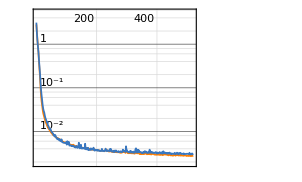
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:5200  rounds:520  time:30s  examples/s:180420
data | ,,  training examples:10000  validation examples:5000  processed examples:5324800  skipped examples:0
method | ,,  ADAMoptimizer  batch size1024CPU
round | ,,  loss:2.82×10^-3
validation | ,,  loss:3.1×10^-3
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

θ: {2.96003,2.96003,2.96003,2.96003,2.96003,2.96003,2.96003,2.96003,2.96003,2.96003,2.12015,2.12015,2.12015,2.12015,2.12015,2.12015,2.12015,2.12015,2.12015,2.12015,2.64883,2.64883,2.64883,2.64883,2.64883,2.64883,2.64883,2.64883,2.64883,2.64883,2.99194,2.99194,2.99194,2.99194,2.99194,2.99194,2.99194,2.99194,2.99194,2.99194,2.75293,2.75293,2.75293,2.75293,2.75293,2.75293,2.75293,2.75293,2.75293,2.75293,2.88711,2.88711,2.88711,2.88711,2.88711,2.88711,2.88711,2.88711,2.88711,2.88711,2.69145,2.69145,2.69145,2.69145,2.69145,2.69145,2.69145,2.69145,2.69145,2.69145,2.83418,2.83418,2.83418,2.83418,2.83418,2.83418,2.83418,2.83418,2.83418,2.83418,2.87516,2.87516,2.87516,2.87516,2.87516,2.87516,2.87516,2.87516,2.87516,2.87516,2.26314,2.26314,2.26314,2.26314,2.26314,2.26314,2.26314,2.26314,2.26314,2.26314,2.40686,2.40686,2.40686,2.40686,2.40686,2.40686,2.40686,2.40686,2.40686,2.40686,2.5423,2.5423,2.5423,2.5423,2.5423,2.5423,2.5423,2.5423,2.5423,2.5423,2.54454,2.54454,2.54454,2.54454,2.54454,2.54454,2.54454,2.54454,2.54454,2.54454,2.40928,2.40928,2.40928,2.40928,2.40928,2.40928,2.40928,2.40928,2.40928,2.40928,2.74253,2.74253,2.74253,2.74253,2.74253,2.74253,2.74253,2.74253,2.74253,2.74253,2.82945,2.82945,2.82945,2.82945,2.82945,2.82945,2.82945,2.82945,2.82945,2.82945,2.26137,2.26137,2.26137,2.26137,2.26137,2.26137,2.26137,2.26137,2.26137,2.26137,2.92836,2.92836,2.92836,2.92836,2.92836,2.92836,2.92836,2.92836,2.92836,2.92836,2.37439,2.37439,2.37439,2.37439,2.37439,2.37439,2.37439,2.37439,2.37439,2.37439,2.70652,2.70652,2.70652,2.70652,2.70652,2.70652,2.70652,2.70652,2.70652,2.70652}

θ̂: {2.97601,2.93846,2.97718,2.87709,2.94792,2.86676,2.9228,2.98357,2.93068,2.95727,2.12284,2.17442,2.18313,2.09425,2.14057,2.13006,2.16818,2.17605,2.06557,2.06576,2.70772,2.6779,2.61483,2.62509,2.70456,2.71843,2.56264,2.6668,2.60451,2.69295,2.9973,2.95864,2.96082,2.94815,2.94038,2.92269,2.99025,3.01555,2.97727,3.03119,2.77493,2.747,2.68799,2.69072,2.76359,2.77557,2.7243,2.71786,2.92962,2.73914,2.90275,2.89406,2.88684,2.93645,2.86936,2.86944,2.91011,2.93634,2.74853,2.89756,2.62902,2.71292,2.65611,2.63641,2.68799,2.6948,2.74418,2.75254,2.70614,2.69256,2.8694,2.86726,2.91873,2.83594,2.86226,2.91327,2.88174,2.76414,2.88634,2.72627,2.85568,2.91,2.91929,2.94548,2.9114,2.93073,2.83419,2.9327,2.92997,2.88813,2.23383,2.25154,2.28498,2.35087,2.24479,2.30982,2.23713,2.27675,2.35639,2.31277,2.32646,2.49924,2.37942,2.37637,2.32686,2.49911,2.41603,2.40398,2.38065,2.4624,2.54826,2.46555,2.46413,2.5386,2.6215,2.5245,2.59718,2.45595,2.59592,2.48406,2.42767,2.57636,2.49774,2.66375,2.55099,2.52957,2.4843,2.58872,2.54278,2.59363,2.43201,2.37606,2.47392,2.32653,2.38956,2.43265,2.55288,2.41372,2.42677,2.48969,2.72494,2.76013,2.74573,2.72051,2.71768,2.6794,2.72571,2.74159,2.69951,2.69757,2.85342,2.87307,2.88591,2.86266,2.7585,2.81417,2.80374,2.67449,2.81282,2.88897,2.3642,2.26677,2.142,2.28259,2.32157,2.18464,2.2177,2.26304,2.29301,2.18827,2.97025,2.95202,2.94577,2.84028,2.89676,2.89454,2.97288,2.97864,2.91267,2.84095,2.36561,2.47701,2.3735,2.40766,2.29942,2.42489,2.43296,2.38914,2.36111,2.38586,2.76543,2.63272,2.78443,2.67357,2.66503,2.68195,2.71281,2.73316,2.70356,2.67349}

abs(θ-θ̂): {0.0159827,0.0215708,0.0171555,0.0829407,0.0121111,0.0932647,0.037234,0.023538,0.0293526,0.00275865,0.00268981,0.0542674,0.0629742,0.0259009,0.0204177,0.00990484,0.0480227,0.0558972,0.0545826,0.0543905,0.0588816,0.0290655,0.034007,0.023744,0.055725,0.0695933,0.0861937,0.0179707,0.0443274,0.0441187,0.00536786,0.0332934,0.0311204,0.0437836,0.0515558,0.0692419,0.00168433,0.0236186,0.014665,0.0392555,0.021997,0.00592662,0.0649421,0.0622048,0.0106585,0.0226426,0.0286272,0.0350652,0.176691,0.0137873,0.0156473,0.00695287,0.000270018,0.0493411,0.0177494,0.0176681,0.0230082,0.0492319,0.138578,0.0104543,0.0624275,0.0214758,0.0353367,0.0550387,0.00345612,0.00335836,0.0527306,0.0610979,0.0146923,0.00111961,0.0352153,0.0330755,0.0845486,0.00175705,0.0280742,0.0790819,0.0475573,0.0700444,0.0521552,0.107914,0.019486,0.0348322,0.0441277,0.0703139,0.0362336,0.0555701,0.040973,0.057538,0.054811,0.0129671,0.0293044,0.0115939,0.0218474,0.0877344,0.0183486,0.0466863,0.0260085,0.0136107,0.0932571,0.0496284,0.0804065,0.092381,0.0274382,0.0304938,0.080004,0.0922532,0.00916358,0.00287871,0.0262168,0.0555398,0.00596805,0.076747,0.078167,0.00369911,0.0792028,0.0177975,0.0548882,0.0863493,0.0536253,0.058235,0.116873,0.0318161,0.0467991,0.119207,0.00644574,0.0149757,0.0602395,0.0441793,0.00176492,0.0490817,0.022731,0.0332218,0.0646393,0.0827537,0.0197237,0.0233704,0.143599,0.00443594,0.0174836,0.080404,0.0175887,0.0176055,0.00320569,0.0220188,0.0248414,0.0631247,0.0168134,0.000935642,0.043018,0.0449525,0.0239774,0.0436191,0.0564608,0.0332145,0.0709482,0.0152789,0.0257114,0.15496,0.0166284,0.0595202,0.102828,0.00539711,0.119376,0.0212188,0.0601988,0.0767348,0.0436759,0.00166777,0.0316375,0.073107,0.04189,0.0236638,0.0174118,0.0880756,0.031605,0.0338222,0.0445154,0.0502787,0.0156881,0.0874104,0.00877422,0.102627,0.000880653,0.0332735,0.0749699,0.0504997,0.0585752,0.0147529,0.0132787,0.0114761,0.0589153,0.0737968,0.0779178,0.0329447,0.0414815,0.0245629,0.00629326,0.0266468,0.00295524,0.0330272}

RMSE:0.0528492

```mathematica
{Θ, e} = RunExperiment[PoissonDistribution, {2,3}];
```

### Geometric distribution

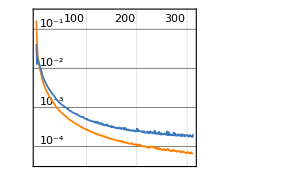
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:3120  rounds:312  time:27s  examples/s:122106
data | ,,  training examples:10000  validation examples:5000  processed examples:3194880  skipped examples:0
method | ,,  ADAMoptimizer  batch size1024CPU
round | ,,  loss:6.7×10^-5
validation | ,,  loss:2.06×10^-4
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

θ: {0.224113,0.224113,0.224113,0.224113,0.224113,0.224113,0.224113,0.224113,0.224113,0.224113,0.254109,0.254109,0.254109,0.254109,0.254109,0.254109,0.254109,0.254109,0.254109,0.254109,0.249164,0.249164,0.249164,0.249164,0.249164,0.249164,0.249164,0.249164,0.249164,0.249164,0.249534,0.249534,0.249534,0.249534,0.249534,0.249534,0.249534,0.249534,0.249534,0.249534,0.205745,0.205745,0.205745,0.205745,0.205745,0.205745,0.205745,0.205745,0.205745,0.205745,0.211391,0.211391,0.211391,0.211391,0.211391,0.211391,0.211391,0.211391,0.211391,0.211391,0.236132,0.236132,0.236132,0.236132,0.236132,0.236132,0.236132,0.236132,0.236132,0.236132,0.270628,0.270628,0.270628,0.270628,0.270628,0.270628,0.270628,0.270628,0.270628,0.270628,0.207318,0.207318,0.207318,0.207318,0.207318,0.207318,0.207318,0.207318,0.207318,0.207318,0.208457,0.208457,0.208457,0.208457,0.208457,0.208457,0.208457,0.208457,0.208457,0.208457,0.288299,0.288299,0.288299,0.288299,0.288299,0.288299,0.288299,0.288299,0.288299,0.288299,0.254819,0.254819,0.254819,0.254819,0.254819,0.254819,0.254819,0.254819,0.254819,0.254819,0.236091,0.236091,0.236091,0.236091,0.236091,0.236091,0.236091,0.236091,0.236091,0.236091,0.23806,0.23806,0.23806,0.23806,0.23806,0.23806,0.23806,0.23806,0.23806,0.23806,0.206968,0.206968,0.206968,0.206968,0.206968,0.206968,0.206968,0.206968,0.206968,0.206968,0.229607,0.229607,0.229607,0.229607,0.229607,0.229607,0.229607,0.229607,0.229607,0.229607,0.284679,0.284679,0.284679,0.284679,0.284679,0.284679,0.284679,0.284679,0.284679,0.284679,0.221957,0.221957,0.221957,0.221957,0.221957,0.221957,0.221957,0.221957,0.221957,0.221957,0.269975,0.269975,0.269975,0.269975,0.269975,0.269975,0.269975,0.269975,0.269975,0.269975,0.290637,0.290637,0.290637,0.290637,0.290637,0.290637,0.290637,0.290637,0.290637,0.290637}

θ̂: {0.208571,0.235056,0.235619,0.219293,0.231971,0.21705,0.222409,0.222074,0.228996,0.21674,0.26508,0.23906,0.238877,0.26111,0.248332,0.285633,0.242724,0.270001,0.226324,0.222919,0.233778,0.25996,0.234446,0.217211,0.26983,0.237916,0.281196,0.254,0.222708,0.267296,0.245203,0.237404,0.256386,0.249815,0.246892,0.256598,0.287709,0.257804,0.234196,0.304751,0.213972,0.222614,0.218108,0.190297,0.200697,0.202865,0.208507,0.213199,0.21608,0.204242,0.222712,0.204312,0.221167,0.221836,0.213729,0.207757,0.203642,0.216667,0.214975,0.214582,0.248509,0.24115,0.251997,0.260181,0.227141,0.253907,0.220512,0.260162,0.2219,0.268354,0.259714,0.263046,0.276526,0.287492,0.26585,0.270379,0.27419,0.265034,0.279019,0.263881,0.206533,0.23138,0.197595,0.219733,0.230119,0.215549,0.207911,0.201939,0.223309,0.218062,0.203348,0.245532,0.20859,0.211546,0.208917,0.218076,0.213268,0.216525,0.215057,0.195553,0.291653,0.28736,0.286444,0.287695,0.274999,0.291527,0.300631,0.284603,0.285124,0.298106,0.247759,0.279927,0.274997,0.258986,0.262614,0.257643,0.265663,0.255314,0.257308,0.232628,0.211872,0.227476,0.267748,0.208343,0.266511,0.230776,0.247066,0.20198,0.239627,0.239873,0.264422,0.227062,0.255385,0.279852,0.258358,0.224747,0.195126,0.253124,0.226583,0.222205,0.208159,0.211132,0.204075,0.217105,0.212245,0.211074,0.209172,0.208946,0.223649,0.210406,0.248148,0.24497,0.222527,0.214656,0.216079,0.235036,0.223927,0.22257,0.233598,0.236489,0.276062,0.28488,0.282713,0.288203,0.286412,0.274563,0.283001,0.289358,0.295368,0.296025,0.222994,0.231886,0.237977,0.229073,0.229519,0.216543,0.238699,0.225314,0.215745,0.245779,0.265216,0.26966,0.26726,0.267868,0.282969,0.277316,0.238122,0.266175,0.277759,0.289297,0.286242,0.280924,0.294582,0.281948,0.29471,0.290428,0.300749,0.29421,0.2942,0.293412}

abs(θ-θ̂): {0.0155417,0.0109431,0.0115063,0.00481915,0.00785804,0.00706299,0.00170397,0.00203838,0.00488333,0.00737273,0.0109711,0.0150487,0.0152321,0.0070004,0.0057769,0.0315234,0.0113852,0.0158921,0.0277856,0.0311902,0.0153859,0.0107965,0.0147179,0.0319527,0.0206664,0.0112475,0.0320327,0.00483683,0.0264556,0.0181326,0.00433162,0.0121299,0.0068523,0.000281242,0.00264216,0.00706368,0.0381747,0.00826964,0.0153379,0.0552165,0.00822702,0.0168684,0.0123623,0.0154482,0.00504845,0.00288004,0.00276217,0.00745353,0.0103352,0.00150329,0.0113204,0.00707904,0.00977527,0.0104449,0.00233715,0.00363404,0.00774966,0.00527602,0.00358357,0.00319075,0.0123771,0.00501878,0.0158653,0.024049,0.00899049,0.017775,0.0156198,0.0240301,0.0142316,0.0322224,0.0109133,0.00758212,0.00589869,0.0168646,0.00477725,0.000248994,0.00356213,0.00559353,0.00839097,0.00674712,0.000785055,0.0240624,0.00972298,0.012415,0.0228013,0.00823101,0.000593242,0.00537908,0.0159916,0.0107441,0.00510904,0.0370748,0.000133484,0.00308952,0.00045973,0.00961882,0.00481132,0.00806859,0.00659975,0.0129035,0.0033538,0.000939402,0.00185576,0.000604602,0.0133007,0.00322747,0.0123313,0.00369665,0.00317574,0.00980672,0.00706072,0.025108,0.0201779,0.00416689,0.00779431,0.00282412,0.0108438,0.000494203,0.00248905,0.0221914,0.0242197,0.00861487,0.0316569,0.0277485,0.0304199,0.00531512,0.0109744,0.0341109,0.0035359,0.00378147,0.0263622,0.0109977,0.0173254,0.0417919,0.0202982,0.0133126,0.0429341,0.0150642,0.0114767,0.0158552,0.00119036,0.00416344,0.00289277,0.0101367,0.00527691,0.00410547,0.00220424,0.00197798,0.0166808,0.00343814,0.0185414,0.0153629,0.00707999,0.0149512,0.0135273,0.00542915,0.00567976,0.00703642,0.00399169,0.00688279,0.00861707,0.000200452,0.001966,0.00352305,0.00173205,0.0101162,0.0016785,0.004679,0.0106882,0.011346,0.00103705,0.00992899,0.01602,0.0071166,0.00756212,0.00541345,0.0167425,0.00335689,0.00621171,0.0238223,0.00475946,0.000315304,0.0027154,0.00210738,0.0129938,0.00734094,0.0318536,0.00379985,0.00778434,0.0193219,0.00439498,0.00971369,0.00394445,0.00868992,0.00407212,0.000209576,0.0101114,0.00357234,0.00356274,0.00277444}

RMSE:0.0144063

```mathematica
{Θ, e} = RunExperiment[GeometricDistribution, {0.2,0.3}];
```